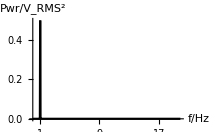

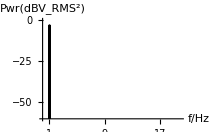

square THD = 1.20927

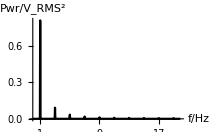

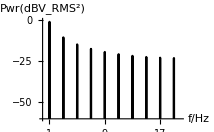

triangle THD = 1.01545

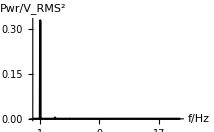

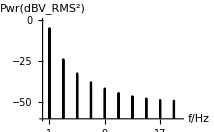

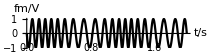

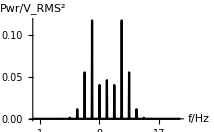

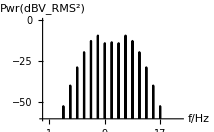

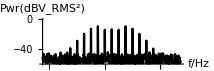

```mathematica
ClearAll[f,sr,len,sin,fsin,sint,rec,frec,rect,tri,ftri,trit,fm,ffm,fmt]
f=1;sr=40;len=1000;
(* sin *)
sin=Table[Sin[2π f/sr n],{n,0,len-1}];
fsin=Fourier[sin,FourierParameters->{-1, 1}]*√2;
sint=Table[{(n*sr)/len, (Abs[fsin[[n+1]]])^2},{n,0,999}];
ListLinePlot[sint[[1;;499]],PlotRange->{0.5,0},AxesOrigin->{0,0},PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},AxesLabel->{"f/Hz","Pwr/V_RMS^2"}]
Periodogram[sin*√2,SampleRate->40,AxesOrigin->{0,-60},FourierParameters->{-1,1},PlotStyle->{Black},AxesStyle->Black,AxesLabel->{"f/Hz","Pwr(dBV_RMS^2)"},PlotRange->{-60,0},Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic}]
(* rect *)
rec=Table[SquareWave [f/sr n],{n,0,len-1}];
frec=Fourier[rec,FourierParameters->{-1, 1}]*√2;
rect=Table[{(n*sr)/len, (Abs[frec[[n+1]]])^2},{n,0,999}];
Print["square THD = ", (√(Total[Abs[frec]^2]-Abs[frec[[26]]]^2))/Abs[frec[[26]]]]
ListLinePlot[rect[[1;;499]],PlotRange->{.85,0},AxesOrigin->{0,0},PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},AxesLabel->{"f/Hz","Pwr/V_RMS^2"}]
Periodogram[rec*√2,SampleRate->40,AxesOrigin->{0,-60},FourierParameters->{-1,1},PlotStyle->{Black},AxesStyle->Black,AxesLabel->{"f/Hz","Pwr(dBV_RMS^2)"},PlotRange->{-60,0},Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic}]
(* tri *)
tri=Table[N[TriangleWave[f/sr n]],{n,0,len-1}];
ftri=Fourier[tri,FourierParameters->{-1, 1}]*√2;
trit=Table[{(n*sr)/len, (Abs[ftri[[n+1]]])^2},{n,0,999}];
Print["triangle THD = ", (√(Total[Abs[ftri]^2]-Abs[ftri[[26]]]^2))/Abs[ftri[[26]]]]
ListLinePlot[trit[[1;;499]],PlotRange->{0.4,0},AxesOrigin->{0,0},PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},AxesLabel->{"f/Hz","Pwr/V_RMS^2"}]
Periodogram[tri*√2,SampleRate->40,AxesOrigin->{0,-60},FourierParameters->{-1,1},PlotStyle->{Black},AxesStyle->Black,AxesLabel->{"f/Hz","Pwr(dBV_RMS^2)"},PlotRange->{-60,0},Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic}]
(* fm *)
fmfunc[t_]:=N[Sin[20π t-π Cos[2π t]]];
fm=Table[N[fmfunc[f/sr n]],{n,0,len-1}];
ffm=Fourier[fm,FourierParameters->{-1, 1}]*√2;
tfm=Table[{(n*sr)/len, (Abs[ffm[[n+1]]])^2},{n,0,999}];
Plot[fmfunc[t],{t,0,2},PlotTheme->"Monochrome",AxesLabel->{"t/s","fm/V"},AspectRatio->0.25]
ListLinePlot[tfm[[1;;499]],PlotRange->{0.2,0},AxesOrigin->{0,0},PlotTheme->"Monochrome",PlotMarkers->None,Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},AxesLabel->{"f/Hz","Pwr/V_RMS^2"}]
Periodogram[fm*√2,SampleRate->40,AxesOrigin->{0,-60},FourierParameters->{-1,1},PlotStyle->{Black},AxesStyle->Black,AxesLabel->{"f/Hz","Pwr(dBV_RMS^2)"},PlotRange->{-60,0},Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic}]
(* with noise *)
fmnoi=Table[N[fmfunc[f/sr n]]+RandomReal[{-0.1,0.1}],{n,0,len-1}];
Periodogram[fmnoi*√2,SampleRate->40,AxesOrigin->{0,-60},FourierParameters->{-1,1},PlotStyle->{Black},AxesStyle->Black,AxesLabel->{"f/Hz","Pwr(dBV_RMS^2)"},PlotRange->{-60,0},Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},AspectRatio->1/3,PlotStyle->Thin]
```

```mathematica
N[(√(∑_(i=1)^∞ (1/(2 i+1))^2))/1]
N[(√(∑_(i=1)^∞ (1/(2 i+1)^2)^2))/1]
```

0.483426

0.121153